```mathematica
ClearAll["Global'*"];

Ep1 = m * g * H;
Ep2 = m * g * (2 * R);
Ek = (m * v^2)/2;

Fg = m*g;
Fod = (m*v^2)/R;

r1 = Solve[{Fg == Fod, Ep2 == Ep1-Ek},{v, R}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{v→-1.98091 √H,R→0.4 H},{v→1.98091 √H,R→0.4 H}}

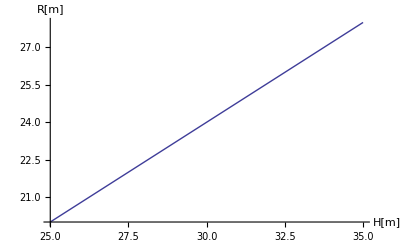

```mathematica
Plot[2R /.r1[[1,2]],{H,25,35},
AxesLabel->{"H[m]", "R[m]"}, AxesOrigin->{25,20}]
```